```mathematica
<<Units`
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

#### Without Pauli-Blocking

```mathematica
f[θ_]:=k-k/(1+(k (1-Cos[θ]))/me)
dσdΩ=α^2/me^2 P^2/2(P+1/P-Sin[θ]^2)/.P->1/(1+k/me(1-Cos[θ]));
comptontrial=1/(3 k^2 me (2 k+me)^3)π α^2 (2 k (-10 k^4+51 k^3 me+93 k^2 me^2+51 k me^3+9 me^4)+3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-2 k-me]-3 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[-me]);
comptontest=LogLogPlot[n comptontrial(5.*^5)/.{me->0.5,α->1/137,n->8},{k,10^-1,10^10},PlotStyle->Dashed];
```

#### With Pauli-Blocking:

```mathematica
α^2/me^2 P^2/2(P+1/P-Sin[θ]^2)/.P->1/(1+k/me(1-Cos[θ]))/.Cos[θ]->x
```

(α^2 (1+1/(1+(k (1-x))/me)+(k (1-x))/me-Sin[θ]^2))/(2 me^2 (1+(k (1-x))/me)^2)

```mathematica
ff[x_]:=f[θ]/.Cos[θ]->x
dσdx=(α^2 (1+1/(1+(k (1-x))/me)+(k (1-x))/me-(1-x^2)))/(2 me^2 (1+(k (1-x))/me)^2)*2Pi;
Solve[ff[x]==Ef,x]//FullSimplify
```

{{x→1+(Ef me)/((Ef-k) k)}}

```mathematica
comptonnon=Integrate[dσdx*ff[x]n,x,Assumptions->{k>Ef>0,me>0}];
comptonpauli=Integrate[dσdx*ff[x]*n(ff[x]/Ef),x,Assumptions->{me>0}];
```

```mathematica
pauli1=comptonpauli/.x->1+(Ef me)/((Ef-k) k);
pauli2=comptonpauli/.x->1;
pauli1non=comptonnon/.x->-1;
pauli2non=comptonnon/.x->1+(Ef me)/((Ef-k) k);
paulihard=comptonpauli/.x->-1;
comptontot=(pauli1non-pauli2non)+(pauli1-pauli2);//Simplify
comptontotpauli=(paulihard-pauli2);//Simplify
comptonfull=If[k>Ef,1/(12 Ef k^4 me (2 k+me)^3)n π α^2 (12 k^3 (2 k+me)^3 (k^2-2 k me-4 me^2) Log[me]-12 k^2 (2 k+me)^3 (k (k^2-2 k me-4 me^2)+Ef (-k^2+2 k me+3 me^2)) Log[(k me)/(-Ef+k)]+Ef (-Ef^3 k (2 k+me)^3+2 Ef^2 (k+me)^2 (2 k+me)^3-6 Ef k (2 k+me)^3 (k^2-2 k me-2 me^2)+4 k^2 (44 k^5-114 k^4 me-336 k^3 me^2-279 k^2 me^3-96 k me^4-12 me^5)-12 k^2 (2 k+me)^3 (k^2-2 k me-3 me^2) Log[2 k+me])),1/(3 Ef k me (2 k+me)^4)n π α^2 (2 k (34 k^5-92 k^4 me-283 k^3 me^2-247 k^2 me^3-90 k me^4-12 me^5)+3 (2 k+me)^4 (k^2-2 k me-4 me^2) Log[me]-3 (2 k+me)^4 (k^2-2 k me-4 me^2) Log[2 k+me])];
```

#### Manually cut off compton stopping power when k<Ef to account for target motion of electron.

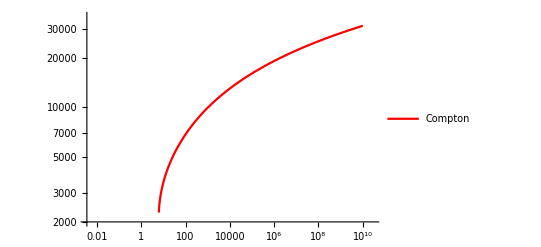

```mathematica
compton=LogLogPlot[ReplaceAll[-comptontot(5.*^5)/.{me->0.5,α->1/137,Ef->(3 Pi^2 n)^(1/3)},n->8],{k,10^-2,10^10},PlotLegends->{"Compton"},PlotStyle->{Red,Thick}];
compton2=LogLogPlot[ReplaceAll[-comptontot(5.*^5)/.{me->0.5,α->1/137,Ef->(3 Pi^2 n)^(1/3)},n->0.032],{k,10^-2,10^10},PlotLegends->{"Compton"},PlotStyle->{Red,Thick}];
Show[compton]
```

#### Full Klein-Nishina scattering cross section (averaged over scattering angles). k=ω/m_e

```mathematica
σ=2Pi α^2/me^2((1+k)/k^2((2(1+k))/(1+2k)-Log[1+2k]/k)+Log[1+2k]/(2k)-(1+3k)/(1+2k)^2);
```

#### Two limits:

```mathematica
Normal[Series[σ,{k,0,0}]]
```

(8 π α^2)/(3 me^2)

```mathematica
FullSimplify[Normal[Series[σ/.k->1/x,{x,0,1}]]/.x->me/ω]
```

(π α^2 (1+Log[4]-2 Log[me/ω]))/(2 me ω)